## advection1_LF

{f→Function[{x,t},1. ⅇ^(-t-10. (-1.+ⅇ^-t x)^2-10. (1.+ⅇ^-t x)^2) (1. ⅇ^(10. (-1.+ⅇ^-t x)^2)+1. ⅇ^(10. (1.+ⅇ^-t x)^2))]}

1. ⅇ^(-t-10. (-1.+ⅇ^-t x)^2-10. (1.+ⅇ^-t x)^2) (1. ⅇ^(10. (-1.+ⅇ^-t x)^2)+1. ⅇ^(10. (1.+ⅇ^-t x)^2))

{True}

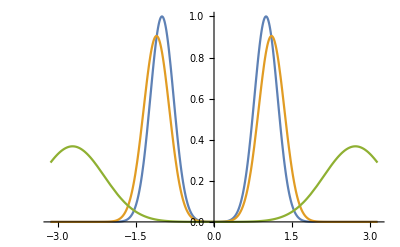

```mathematica
ClearAll["Global`*"];
eq=D[f[x,t],t]==-D[x f[x,t],x];
sig=0.1;
f0=Exp[-(x-1)^2/sig]+Exp[-(x+1)^2/sig];
sol = DSolve[{eq,f[x,0]==f0},f,{x,-Pi,Pi},{t,0,1}];
sol[[1]]
ff[x_,t_]=f[x,t]/.sol[[1]]
FullSimplify[eq/.sol]
Plot[{ff[x,0],ff[x,0.1],ff[x,1]},{x,-Pi, Pi}]
```

{{f→Function[{x,t},(C[1][t-Log[x]])/x]}}

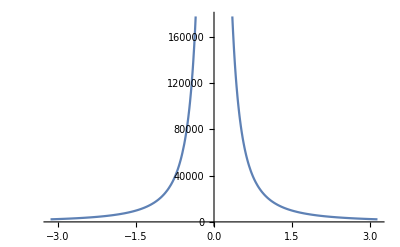

0

```mathematica
ClearAll["Global`*"];
eq=D[f[x,t],t]==-D[x f[x,t],x];
sig=0.1;
f0=Exp[-x^2/sig];
sol = DSolve[{eq},f,{x,t}]
myfun[x_,t_]=Exp[(t-Log[x])]/x;
Plot[myfun[x,t]/.t->10,{x,-Pi,Pi}]
D[myfun[x,t],t]+D[x myfun[x,t],x]
```

## advection2_LF

```mathematica
ClearAll["Global`*"];
eq=D[f[x,y,t],t]==- D[ x f[x,y,t],x]-  D[ y f[x,y,t],y];
sig=2;
offset = Sqrt[x^2+y^2];
f0=0;(*Exp[-offset^2];*)
ContourPlot[f0,{x,-Pi, Pi},{y,-Pi,Pi}];
(*sol = DSolve[{eq,f[x,y,0]==f0,f[-Pi,y,t]==f0,f[x,Pi,t]==f0},f[x,y,t],{x,-Pi,Pi},{y,-Pi,Pi},{t,0,1}];*)
(*sol = DSolve[{eq},f,{x,y,t}]*)
sol2 = NDSolve[{eq,f[x,y,0]==f0,f[-Pi,y,t]==0,f[Pi,y,t]==0,f[x,-Pi,t]==0,f[x,Pi,t]==0},f,{x,-Pi,Pi},{y,-Pi,Pi},{t,0,1}]
(*sol[[1]];
ff[x_,y_,t_]=f[x,y,t]/.sol[[1]];
FullSimplify[eq/.sol];
ContourPlot[{ff[x,y,0]},{x,-Pi, Pi},{y,-Pi,Pi}]*)
(*nsol=NDSolve[{eq,f[x,y,0]==f0,f[-Pi,y,t]==0,f[x,Pi,t]==0},f,{x,-Pi,Pi},{y,-Pi,Pi},{t,0,1}]
ContourPlot[Evaluate[f[x,y,t]],{x,-Pi, Pi},{y,-Pi,Pi}]*)
```

{{f→InterpolatingFunction[…]}}

```mathematica
ContourPlot[Evaluate[f[x,y,t]/.sol2,{x,-Pi,Pi},{y,-Pi,Pi}]
```

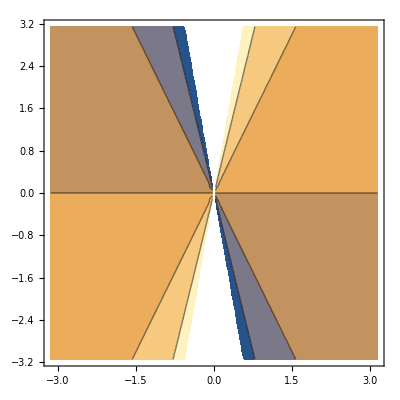

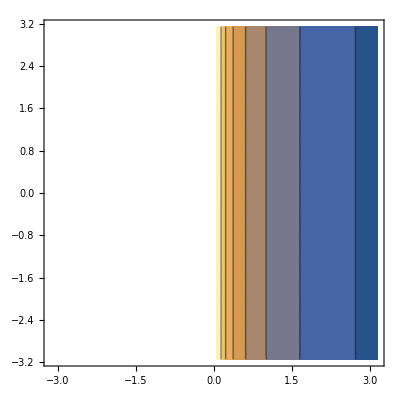

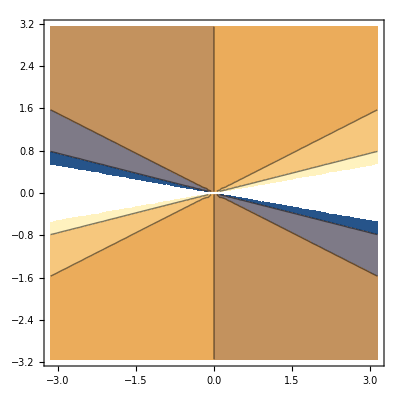

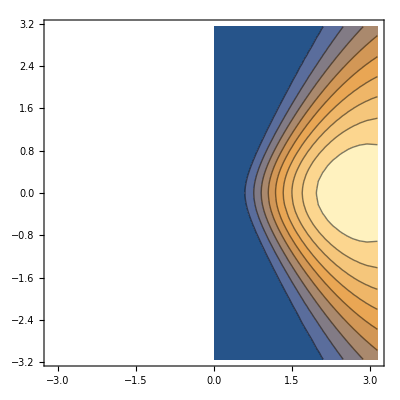

ⅇ^(-y^2/x^2-(t-Log[x])^2)

0

```mathematica
C1[x_,y_]:=Exp[-(x^2 +y^2)];
a=y/x;
b=0-Log[x];
ContourPlot[a,{x,-Pi, Pi},{y,-Pi,Pi}]
ContourPlot[b,{x,-Pi, Pi},{y,-Pi,Pi}]
ContourPlot[1/a,{x,-Pi, Pi},{y,-Pi,Pi}]
ContourPlot[C1[y/x,t-Log[x]]/.t->1,{x,-Pi, Pi},{y,-Pi,Pi}]
CC=C1[y/x,t-Log[x]]
FullSimplify[D[CC,t]+x D[CC,x] + y D[CC,y]]
```